FittedModel[-11.9071+1.85541 x]

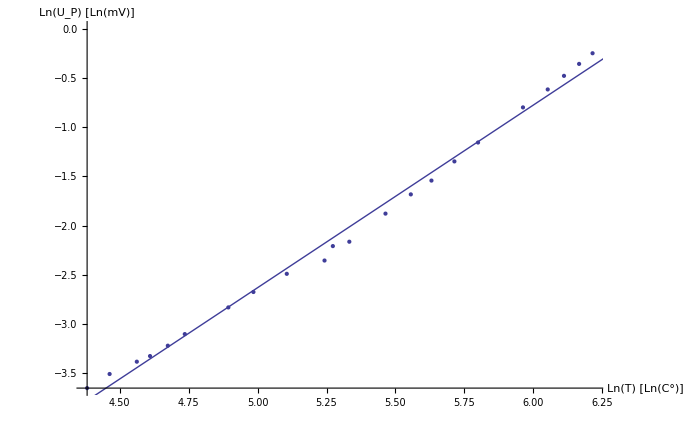

```mathematica
(* Aufgabe 2.1 *)
punkte={{Log[80],Log[0.026]},{Log[86.8],Log[0.03]},{Log[95.8],Log[0.034]},{Log[100.5],Log[0.036]},{Log[107.2],Log[0.04]},{Log[114],Log[0.045]},{Log[133.5],Log[0.059]},{Log[146.2],Log[0.069]},{Log[165],Log[0.083]},{Log[189.2],Log[0.095]},{Log[195],Log[0.11]},{Log[207],Log[0.115]},{Log[236],Log[0.153]},{Log[258.7],Log[0.186]},{Log[278.8],Log[0.214]},{Log[303],Log[0.26]},{Log[330.1],Log[0.315]},{Log[388.5],Log[0.45]},{Log[425],Log[0.54]},{Log[450.8],Log[0.62]},{Log[476.2],Log[0.7]},{Log[500],Log[0.78]}};

model=LinearModelFit[punkte,x,x]
Show[ListPlot[punkte],Plot[model["BestFit"],{x,4,8}],AxesLabel->{"Ln(T) [Ln(C°)]", "Ln(U_P) [Ln(mV)]"}]
```